## 1D

Periodic functions f:(0,2π)->ℝ can be represented by a sum
	a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))
The decay of the Fourier coefficients is determined by the smoothness of the periodic extension of f.
The speed of convergence of this Fourier Series depends on the decay of the Fourier coefficients.
a_n=0 for odd functions and b_n=0 for even functions.

### Example from slides with “jump”

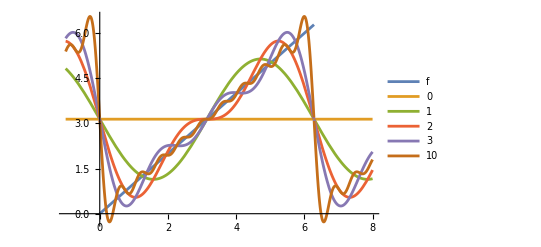

```mathematica
Clear[f,x,a,b,n]
f[x_]:= If[0<x<2π,x]
b[n_]:= -2/n
a[0]:=π;
Plot[
{f[x],π, 
π-2 Sum[1/n Sin[n  x],{n,1,1}],π-2 Sum[1/n Sin[n  x],{n,1,2}],π-2 Sum[1/n Sin[n  x],{n,1,3}],π-2 Sum[1/n Sin[n  x],{n,1,10}]},
{x, -1,8},
PlotLegends->{"f",0,1,2,3,10},
PlotRange->All]
```

### Smooth 2π periodic example

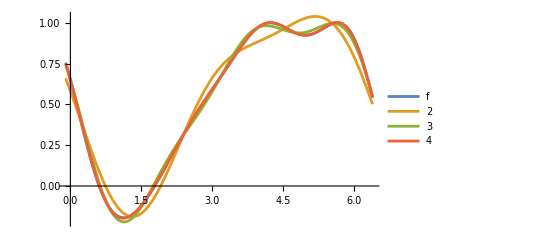

```mathematica
Clear[f,x,a,b,n]
f[x_]:= Cos[Sin[x]+Cos[Cos[x+1]]]
a[0]=1/π NIntegrate[f[x],{x,0, 2π}];
a[n_]:=a[n]=1/π NIntegrate[f[x]Cos[n x],{x,0, 2π}]
b[n_]:=b[n]=1/π NIntegrate[f[x]Sin[n x],{x,0, 2π}]
Plot[
{f[x],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,3}],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,4}]
},
{x, -0.1,2π+0.1},
PlotLegends->{"f",2,3,4},
PlotRange->All]
```

Looking at the error!

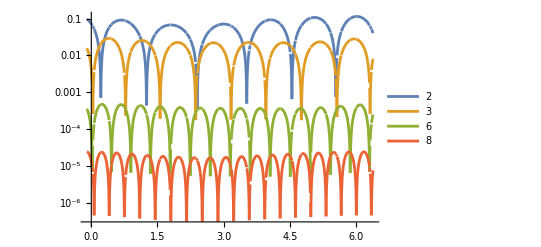

```mathematica
LogPlot[{
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,3}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,6}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,8}]-f[x]]
},
{x, -0.1,2π+0.1},
PlotLegends->{2,3,6,8},
PlotRange->All]
```

## 1D

Periodic functions f:(0,2π)->ℝ can be represented by a sum
	a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))
The decay of the Fourier coefficients is determined by the smoothness of the periodic extension of f.
The speed of convergence of this Fourier Series depends on the decay of the Fourier coefficients.
a_n=0 for odd functions and b_n=0 for even functions.

### Example from slides with “jump”

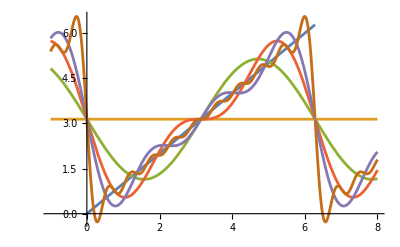

```mathematica
Clear[f,x,a,b,n]
f[x_]:= If[0<x<2π,x]
b[n_]:= -2/n
a[0]:=π;
Plot[
{f[x],π, 
π-2 Sum[1/n Sin[n  x],{n,1,1}],π-2 Sum[1/n Sin[n  x],{n,1,2}],π-2 Sum[1/n Sin[n  x],{n,1,3}],π-2 Sum[1/n Sin[n  x],{n,1,10}]},
{x, -1,8},
PlotRange->All]
```

### Smooth 2π periodic example

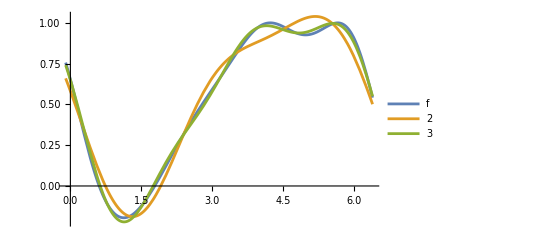

```mathematica
Clear[f,x,a,b,n]
f[x_]:= Cos[Sin[x]+Cos[Cos[x+1]]]
a[0]=1/π NIntegrate[f[x],{x,0, 2π}];
a[n_]:=a[n]=1/π NIntegrate[f[x]Cos[n x],{x,0, 2π}]
b[n_]:=b[n]=1/π NIntegrate[f[x]Sin[n x],{x,0, 2π}]
Plot[
{f[x],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,3}]},
{x, -0.1,2π+0.1},
PlotLegends->{"f",2,3},
PlotRange->All]
```

Looking at the error!

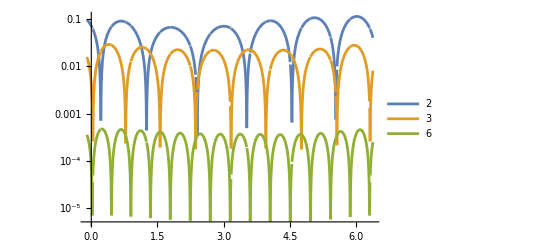

```mathematica
LogPlot[{
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,3}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,6}]-f[x]]},
{x, -0.1,2π+0.1},
PlotLegends->{2,3,6},
PlotRange->All]
```

### Less smooth 2π periodic example

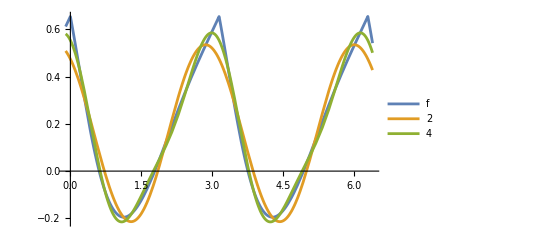

```mathematica
Clear[f,x,a,b,n]
f[x_]:= Cos[Abs[Sin[x]]+Cos[Cos[x+1]]]
a[0]=1/π NIntegrate[f[x],{x,0, 2π}];
a[n_]:=a[n]=1/π NIntegrate[f[x]Cos[n x],{x,0, 2π}]
b[n_]:=b[n]=1/π NIntegrate[f[x]Sin[n x],{x,0, 2π}]
Plot[
{f[x],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}],
a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,4}]},
{x, -0.1,2π+0.1},
PlotLegends->{"f",2,4},
PlotRange->All]
```

Looking at the error!

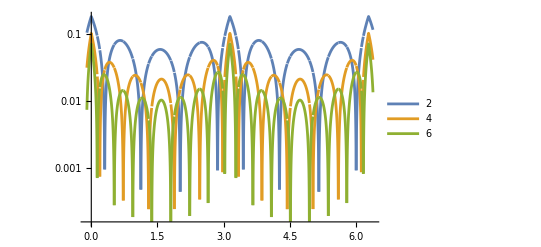

```mathematica
LogPlot[{
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,2}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,4}]-f[x]],
Abs[a[0]/2+Sum[a[n] Cos[n x]+b[n]Sin[n x],{n,1,6}]-f[x]]},
{x, -0.1,2π+0.1},
PlotLegends->{2,4,6},
PlotRange->All]
```